```mathematica
(*Functions*)
Cst[u_]:=0.5*u^2;
Prc[u_]:=a-b*u;
H[u_,μ_,t_]:=(a-b*u)*u-0.5*u^2-μ*u;
dHdu[u_,μ_,t_]:=D[H[u,μ,t],u];
u[T_,r_,t_]:=1/(2*b+1)*(a-S*Exp[r*(t-T)]);
μ[T_,r_,t_]:=S*Exp[r*(t-T)];

(*Y as the integral of u*)
Y[T_,r_]:=Integrate[u[T,r,τ],{τ,0,T}]

(*solving x(t) analytically*)
x[T_,r_]:=-Integrate[u[T,r,τ],{τ,0,T}]

(*Printing values*)
Print["Y(t) = ",Y[T,r]];
Print["x(t) = ",x[T,r]];
```

Y(t) = -(S-ⅇ^(-r T) S-a r T)/(r+2 b r)

x(t) = (S-ⅇ^(-r T) S-a r T)/(r+2 b r)

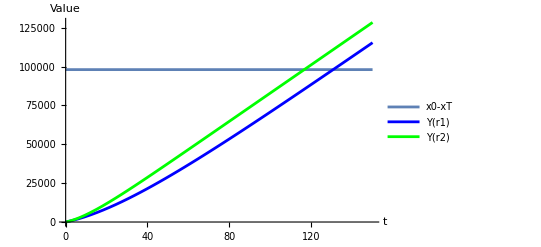

T1(r1): 130.727

T2(r2): 116.605

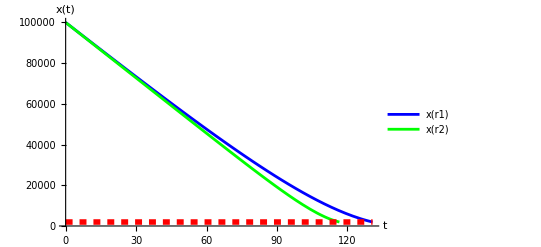

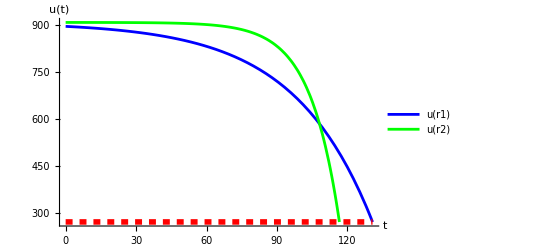

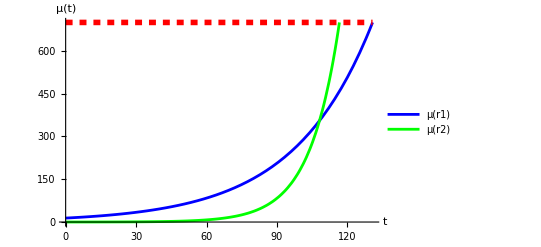

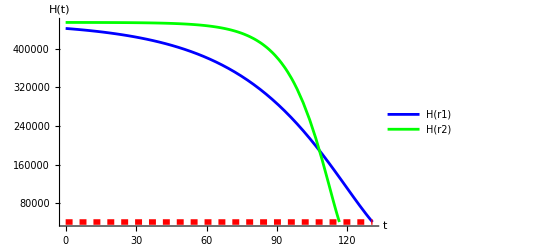

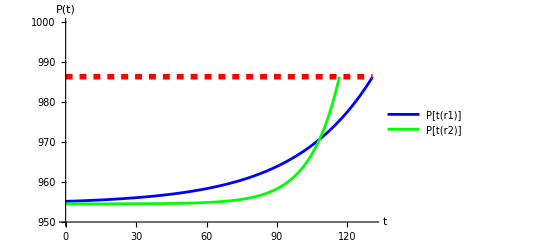

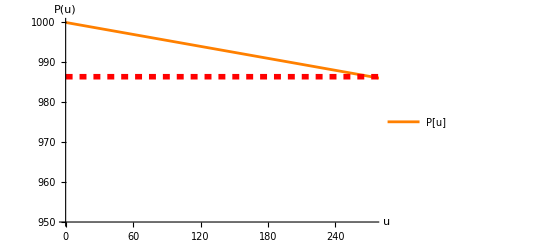

```mathematica
(*Parameters*)
a=1000;
b=0.05;
r1=0.03;
r2=0.08;
x0=100000;
xT = 1949;
S=700;

(*Solving for Optimal T*)
T1=t/. FindRoot[x0-xT-Y[t,r1]==0,{t,120}];
T2=t/. FindRoot[x0-xT-Y[t,r2]==0,{t,120}];
Plot[{x0-xT,Y[t,r1],Y[t,r2]},{t,0,150},PlotStyle->{Automatic,Blue,Green},PlotLegends->{"x0-xT","Y(r1)","Y(r2)"},AxesLabel->{"t","Value"},PlotRange->All]
Print["T1(r1): ",T1];
Print["T2(r2): ",T2];

(*Solving for x with boundary conditions*)
sol1=DSolve[{x'[t]==-u[T1,r1,t],x[0]==x0},x[t],t];
sol2=DSolve[{x'[t]==-u[T2,r2,t],x[0]==x0},x[t],t];

(*Plots*)
Plot[{ConditionalExpression[Evaluate[x[t]/. sol1],t<=T1],ConditionalExpression[Evaluate[x[t]/. sol2],t<=T2]},{t,0,150},PlotStyle->{Blue,Green},PlotLegends->{"x(r1)","x(r2)"},AxesLabel->{"t","x(t)"},PlotRange->{0,All},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,1949},{Max[T1,T2],1949}}]}]

Plot[{ConditionalExpression[u[T1,r1,t],t<=T1],ConditionalExpression[u[T2,r2,t],t<=T2]},{t,0,Max[T1,T2]},PlotStyle->{Blue,Green},PlotLegends->{"u(r1)","u(r2)"},AxesLabel->{"t","u(t)"},PlotRange->{0,All},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,273},{Max[T1,T2],273}}]}]

Plot[{ConditionalExpression[μ[T1,r1,t],t<=T1],ConditionalExpression[μ[T2,r2,t],t<=T2]},{t,0,Max[T1,T2]},PlotStyle->{Blue,Green},PlotLegends->{"μ(r1)","μ(r2)"},AxesLabel->{"t","μ(t)"},PlotRange->{0,All},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,700},{Max[T1,T2],700}}]}]

Plot[{ConditionalExpression[H[u[T1,r1,t],μ[T1,r1,t],t],t<=T1],ConditionalExpression[H[u[T2,r2,t],μ[T2,r2,t],t],t<=T2]},{t,0,Max[T1,T2]},PlotStyle->{Blue,Green},PlotLegends->{"H(r1)","H(r2)"},AxesLabel->{"t","H(t)"},PlotRange->{0,All},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,40909},{Max[T1,T2],40909}}]}]

Plot[{ConditionalExpression[Prc[u[T1,r1,t]],t<=T1],ConditionalExpression[Prc[u[T2,r2,t]],t<=T2]},{t,0,Max[T1,T2]},PlotStyle->{Blue,Green},PlotLegends->{"P[t(r1)]","P[t(r2)]"},AxesLabel->{"t","P(t)"},PlotRange->{{0,Max[T1,T2]},{950,1000}},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,986.4},{Max[T1,T2],986.4}}]}]

Plot[Prc[u/. {a->1000,b->0.05}],{u,0,300},PlotStyle->Orange,PlotLegends->{"P[u]"},AxesLabel->{"u","P(u)"},PlotRange->{{0,273},{950,1000}},Epilog->{Directive[Red,Dashed,Thickness[0.01]],Line[{{0,986.4},{300,986.4}}]}]
```